## Metric

metric:

ds^2= -a(r)dt^2+ dr^2/(b(r))+ r^2 dθ^2+ r^2 sin^2 θ dΩ^2  .

a(r) = b(r) = 1 - (2M)/r+ζ^2/r^2(1-(2M)/r)^2  .

## Lapce function

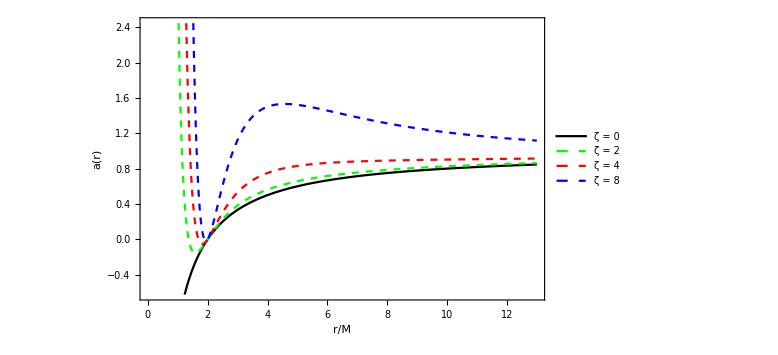

```mathematica
a[r_,ζ_] := 1- 2/r+ζ^2/r^2(1-2/r)^2
Plot[{a[r,0],a[r,2],a[r,4],a[r,8]},{r,0,13},Frame->True,FrameLabel->{"r/M","a(r)"},ImageSize->Large,PlotStyle-> {{Black},{Dashed,Green},{Dashed,Red},{Dashed,Blue}},PlotLegends->Placed[{"ζ = 0","ζ = 2","ζ = 4","ζ = 8"},{Scaled[{0.70,0.5}],{0.8,1.45}}],LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15}]
```

### event horizon

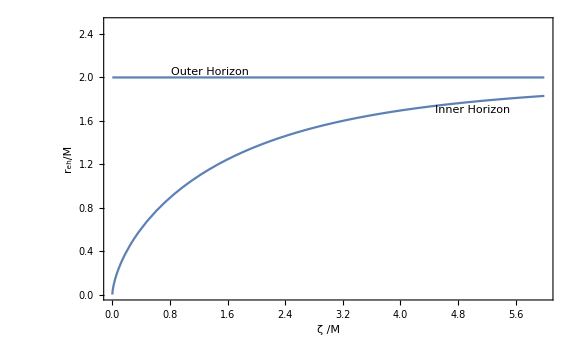

```mathematica
reh[ζ_] = r/.Solve[a[r,ζ]==0,r];
Limit[reh[ζ],ζ->Infinity];

Plot[reh[ζ],{ζ,0,6},PlotRange->{{0,6},{0,2.5}},Frame->True,FrameLabel->{"ζ /M","r_eh/M"},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},Epilog->{Text[Rotate[Framed[Style["Outer Horizon",Italic,Bold],FrameStyle->None,Background->None],0 Degree],{1.35,2.05}],Text[Rotate[Framed[Style["Inner Horizon",Italic,Bold],FrameStyle->None,Background->None],0 Degree],{5,1.7}]},ImageSize->Large]
```

## Effective Potential uchp

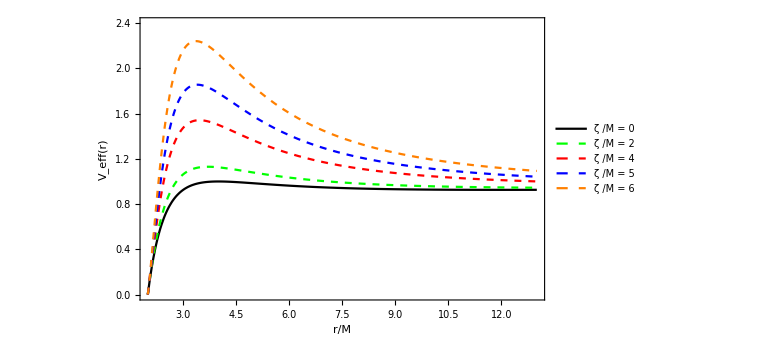

```mathematica
a[r_,ζ_] := 1- 2/r+ζ^2/r^2(1-2/r)^2
Veff[L_,r_,ζ_] := a[r,ζ](1 + L^2/r^2)
veff[Ene_,L_,ζ_,r_] :=-1 - L^2/r^2- Ene^2/a[r,ζ]
Plot[{Veff[4,r,0],Veff[4,r,2],Veff[4,r,4],Veff[4,r,5],Veff[4,r,6]},{r,2,13},PlotRange->{{2,13},{0,2.4}},Frame->True,FrameLabel->{"r/M","V_eff(r)"," ℒ = 4"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Green},{Dashed,Red},{Dashed,Blue},{Dashed,Orange}},PlotLegends->Placed[{"ζ /M = 0","ζ /M = 2","ζ /M = 4","ζ /M = 5","ζ /M = 6"},{Scaled[{0.70,0.5}],{-0.2,-0.1}}],ImageSize->Large]
```

### angular momentum of particle

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partw: Part 13 of {{L→-3.4641,r→6.},{L→3.4641,r→6.}} does not exist.

ReplaceAll::reps: {{{L→-3.4641,r→6.},{L→3.4641,r→6.}}⟦13⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

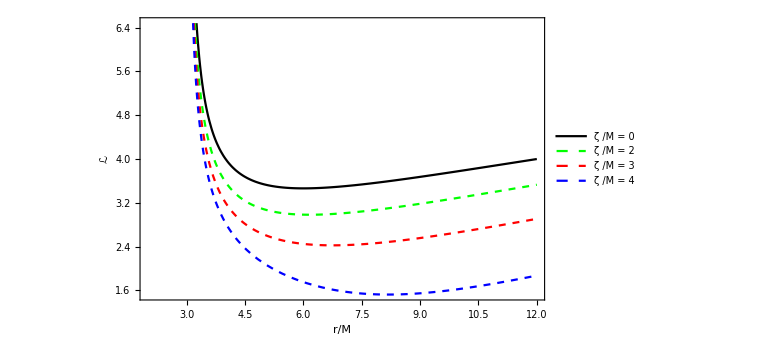

```mathematica
a[r_,ζ_] := 1- 2/r+ζ^2/r^2(1-2/r)^2
ris[ζ_]:=r/.Solve[D[Veff[L,r,ζ],r]==0&&D[Veff[L,r,ζ],r,r]==0,{L,r}][[13]]
L[ζ_,r_]=L/.Solve[D[Veff[L,r,ζ],r]==0,L][[2]];
Ene[ζ_,r_]:=(a[r,ζ] (1+ L[ζ,r]^2/r^2))^0.5
NSolve[D[L[0,r],r]==0,r];
ris[0.]//N;
Plot[{L[0,r],L[2,r],L[3,r],L[4,r]},{r,2,12},Frame->True,FrameLabel->{"r/M","ℒ"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Green},{Dashed,Red},{Dashed,Blue}},PlotLegends->Placed[{"ζ /M = 0","ζ /M = 2","ζ /M = 3","ζ /M = 4"},{Scaled[{0.70,0.5}],{-0.2,-0.1}}],ImageSize->Large]
Plot[Ene[0,r],{r,0,5}];
(*Plot[ris[ζ],{ζ,0,4},Frame->True]*)
```

### energy of particle

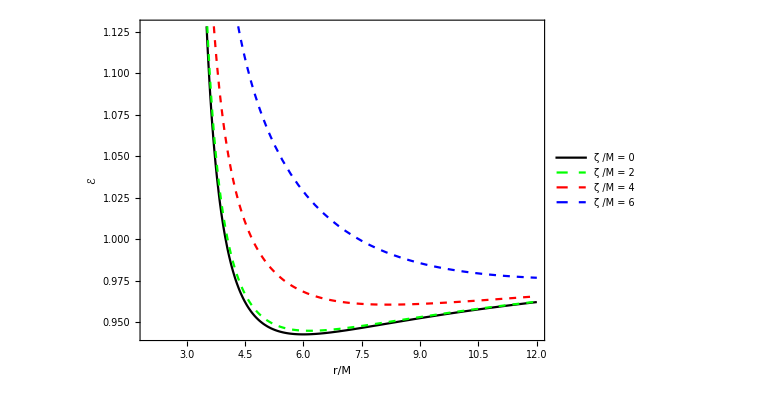

```mathematica
Ene[ζ_,r_]:=(a[r,ζ] (1+ L[ζ,r]^2/r^2))^0.5
Plot[{Ene[0,r],Ene[2,r],Ene[4,r],Ene[6,r]},{r,2,12},Frame->True,FrameLabel->{"r/M","ℰ"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Green},{Dashed,Red},{Dashed,Blue}},PlotLegends->Placed[{"ζ /M = 0","ζ /M = 2","ζ /M = 4","ζ /M = 6"},{Scaled[{0.70,0.5}],{-0.2,-0.1}}],ImageSize->Large,AspectRatio->0.7]
```

### isco

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

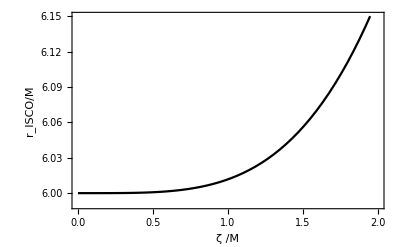

```mathematica
ris[ζ_]:=r/.Solve[D[Veff[L,r,ζ],r]==0&&D[Veff[L,r,ζ],r,r]==0,{L,r}][[13]]
Plot[ris[ζ],{ζ,0,2},PlotRange->{{0,2},{5.99,6.15}},Frame->True,FrameLabel->{"ζ /M","r_ISCO/M"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->Black]
```

## Effective Potential chp

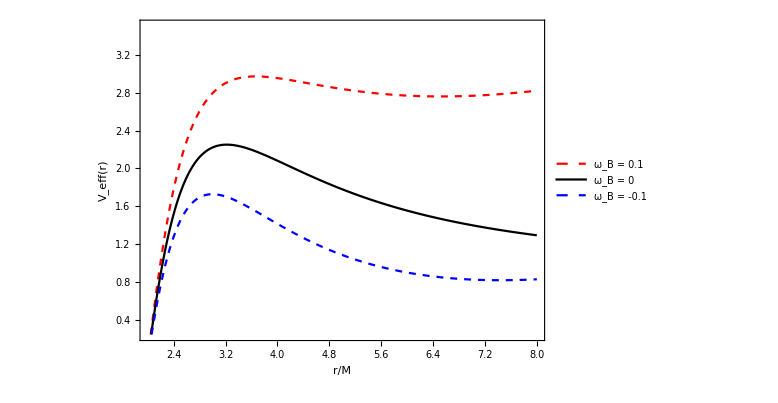

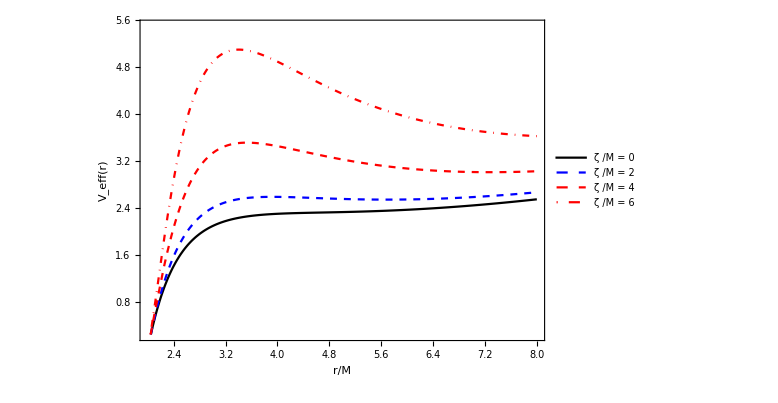

```mathematica
a[r_,ζ_] := 1- 2/r+ζ^2/r^2(1-2/r)^2
Veeff[L_,ω_,r_,ζ_] := a[r ,ζ] (1+(L/r+ ω r)^2)
Plot[{Veeff[6,0.1,r,3],Veeff[6,0,r,3],Veeff[6,-0.1,r,3]},{r,2,8},Frame->True,FrameLabel->{"r/M","V_eff(r)"," ℒ = 6,  ζ /M = 3,   ω_B = qB/(2  mc)"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Dashed,Red},{Black},{Dashed, Blue}},PlotLegends->Placed[{"ω_B = 0.1", "ω_B = 0","ω_B = -0.1"},{Scaled[{0.70,0.5}],{-0.2,-0.1}}],ImageSize->Large,AspectRatio->0.7, PlotRange->{{2.,8},{0.25,3.5}}]


Plot[{Veeff[6,0.1,r,0],Veeff[6,0.1,r,2],Veeff[6,0.1,r,4],Veeff[6,0.1,r,6]},{r,2,8},Frame->True,FrameLabel->{"r/M","V_eff(r)"," ℒ = 6, ω_B = 0.1"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Blue},{Dashed,Red},{DotDashed,Red}},PlotLegends->Placed[{"ζ /M = 0", "ζ /M = 2","ζ /M = 4","ζ /M = 6"},{Scaled[{0.70,0.5}],{-0.2,1.5}}],ImageSize->Large,AspectRatio->0.7,PlotRange->{{2.,8},{0.25,5.5}}]
```

### angular momentum

Solve::svars: Equations may not give solutions for all "solve" variables.

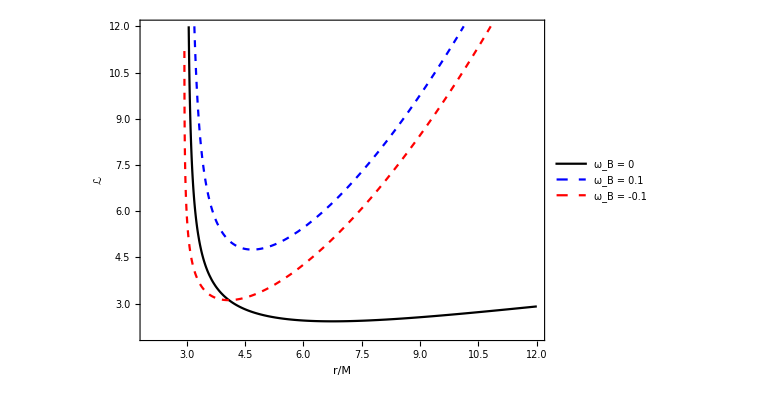

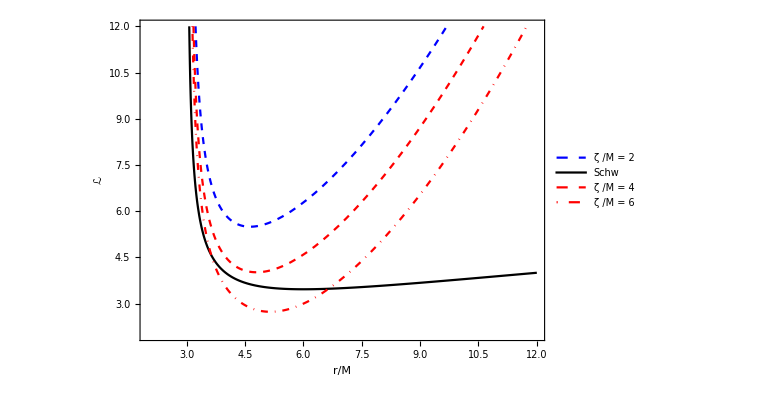

```mathematica
L[r_,ζ_,ω_] =ll/.Solve[D[a[r ,ζ] (1+(ll/r+ ω r)^2),r]==0,{ll,r}][[2]];
Solve[D[L[r,0,0],r]==0,r];
Lb[r_,ζ_,ω_]=If[L[r,3,0]<=5.91904,L[r,3,0],None];
Lr[r_,ζ_,ω_]=If[L[r,3,-0.1]<=5.93704 && r≤2.97,L[r,3,-0.1],None];
Plot[{L[r,3,0],L[r,3,0.1],L[r,3,-0.1]},{r,2,12},PlotRange->{{2,12},{2,12}},Frame->True,FrameLabel->{"r/M","ℒ","ζ /M = 3"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Blue},{Dashed,Red}},PlotLegends->Placed[{"ω_B = 0","ω_B = 0.1","ω_B = -0.1"},{Scaled[{0.70,0.5}],{-0.2,1.5}}],ImageSize->Large,AspectRatio->0.7,PlotRange->{{2.,5},{0.25,5.5}}]


Plot[{L[r,2,0.1],L[r,0,0],L[r,4,0.1],L[r,6,0.1]},{r,2,12},PlotRange->{{2,12},{2,12}},Frame->True,FrameLabel->{"r/M","ℒ","ω_B = 0.1"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Dashed,Blue},{Black},{Dashed,Red},{DotDashed,Red}},PlotLegends->Placed[{"ζ /M = 2","Schw","ζ /M = 4","ζ /M = 6"},{Scaled[{0.70,0.5}],{2.2,-0.5}}],ImageSize->Large,AspectRatio->0.7,PlotRange->{{2.,5},{0.25,5.5}}]
```

### energy

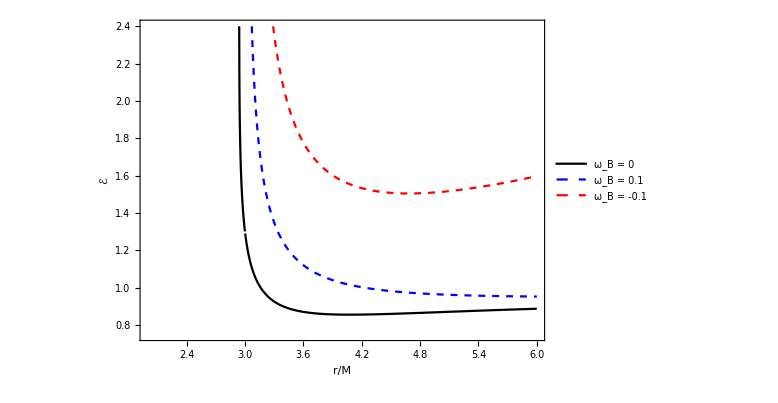

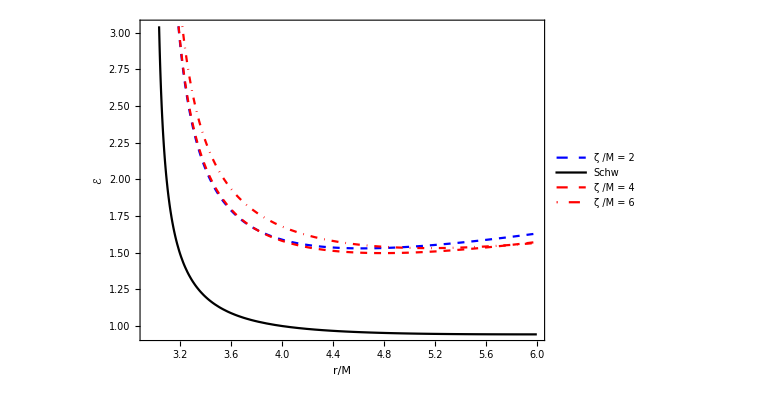

```mathematica
ene[r_,ζ_,ω_]:= (a[r ,ζ] (1+(L[r,ζ,ω]/r+ ω r)^2))^0.5
Plot[ene[r,3,-0.1],{r,2.95,6}];
Plot[{ene[r,3,-0.1],ene[r,3,0],ene[r,3,0.1]},{r,2,6},PlotRange->{{2,6},{0.75,2.4}},Frame->True,FrameLabel->{"r/M","ℰ","ζ /M = 3"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Blue},{Dashed,Red},{DotDashed,Red}},PlotLegends->Placed[{"ω_B = 0","ω_B = 0.1","ω_B = -0.1"},{Scaled[{0.70,0.5}],{-0.2,1.5}}],ImageSize->Large,AspectRatio->0.7]


Plot[{ene[r,2,0.1],ene[r,0,0],ene[r,4,0.1],ene[r,6,0.1]},{r,2.95,6},Frame->True,FrameLabel->{"r/M","ℰ","ω_B = 0.1"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Dashed,Blue},{Black},{Dashed,Red},{DotDashed,Red}},PlotLegends->Placed[{"ζ /M = 2","Schw","ζ /M = 4","ζ /M = 6"},{Scaled[{0.70,0.5}],{2.2,-0.5}}],ImageSize->Large,AspectRatio->0.7]
```

### isco radii dep on ω_B

```mathematica
L1[r_,ζ_,ω_] = D[L[r,ζ,ω],r];
risc[ζ_,ω_]:=r/.FindRoot[L1[r,ζ,ω],{r,6}]
risc[4.55,0]
```

9.44086

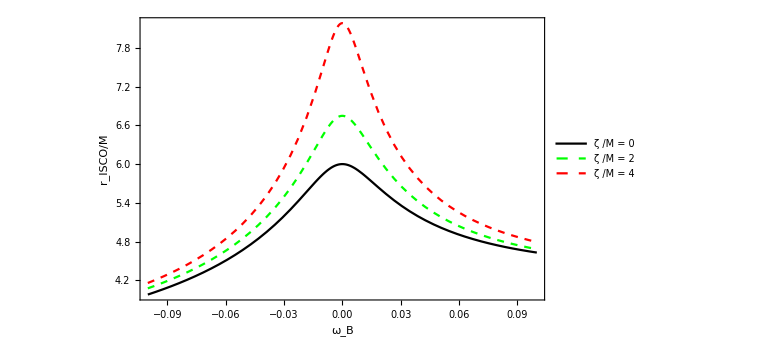

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

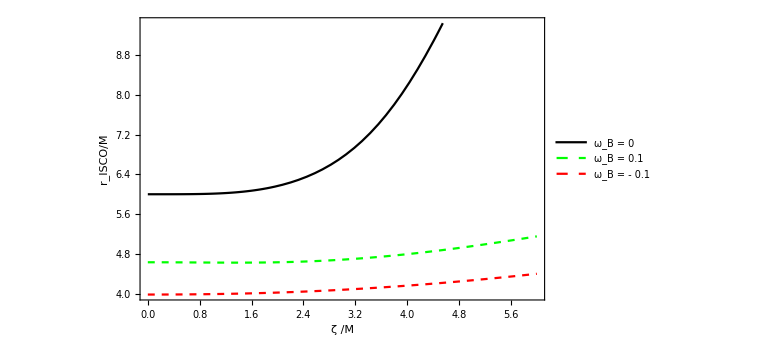

```mathematica
Plot[{risc[0,ω],risc[3,ω],risc[4,ω]},{ω,-0.1,0.1},Frame->True,FrameLabel->{"ω_B","r_ISCO/M"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Green},{Dashed,Red}},PlotLegends->Placed[{"ζ /M = 0","ζ /M = 2","ζ /M = 4"},{Scaled[{0.70,0.5}],{-0.2,-0.2}}],ImageSize->Large]

riscB[ζ_,ω_] = If[ζ<=4.55,risc[ζ,ω],None];

Plot[{riscB[ζ,0],risc[ζ,0.1],risc[ζ,-0.1]},{ζ,0,6},Frame->True,FrameLabel->{"ζ /M","r_ISCO/M"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Green},{Dashed,Red}},PlotLegends->Placed[{"ω_B = 0","ω_B = 0.1","ω_B = - 0.1"},{Scaled[{0.70,0.5}],{-0.2,-0.2}}],ImageSize->Large]
```